## Auxiliary Functions and Definitions

```mathematica
$Assumptions={_∈Reals, h > 0, Vt > 0, d  > 0, A > 0};

printWithBasis[M_,states_]:=(ML=Length[M];
newM=Table[If[(i==0&&j≠0),states[[j]],If[j==0&&i≠0,states[[i]],If[i==0&&j==0,"",M[[i]][[j]]]]],{i,0,ML},{j,0,ML}];
Print[MatrixForm[newM]])
basisGE = {"|g↓⇓>", "|g↓⇑>", "|g↑⇓>", "|g↑⇑>", "|e↓⇓>", "|e↓⇑>", "|e↑⇓>", "|e↑⇑>"};
basisGERotated = {"|g↓⇓>", "|g↓⇑>", "|g↑⇓> + |e↓⇑>", "|g↑⇑>", "|e↓⇓>", "|g↑⇓> - |e↓⇑>", "|e↑⇓>", "|e↑⇑>"};

TProduct[M__]:=KroneckerProduct[M]
σI = PauliMatrix[0];
σX = PauliMatrix[1];
σY = PauliMatrix[2];
σZ = PauliMatrix[3];

Sx=(hBar/2)σX;
Sy=(hBar/2)σY;
Sz=(hBar/2)σZ;

Ix=(hBar/2)σX;
Iy=(hBar/2)σY;
Iz=(hBar/2)σZ;

SdotI=TProduct[Sx,Ix]+TProduct[Sy,Iy]+TProduct[Sz,Iz];

hBar=1;

transform[M_,U_]:=U.M.ConjugateTranspose[U]-ⅈ*hBar*U.ConjugateTranspose[D[U, t]]

(* SI units *)
setVariables[]:=(
ΔE = 0;
B0 = 0.20112299109490023;(* T *)
d=15*10^-9; (* m *)
A=117*10^6; (* Hz *)
γe=27.97*10^9; (* Hz/T *)
γn=17.23*10^6; (* Hz/T *)
Δγ=-.002;
h=6.62607004*10^-34; (* J*s *)
e=-1.60217662*10^-19; (* C *)
Vt = γe*B0 + A/4; (* Hz *)
δB = γe*B0 - νB;

dDip = 400*10^-9; (* m *)

Tmax = 100*10^-9;

(* PARAMETERS OF HIGH-FIDELITY GATE *)
Eamp[t_] := 222.4901014437078 tanhWindow[t,Tmax/10,Tmax]^2 ;
Bamp[t_] := 0.028851198211908263 tanhWindow[t,Tmax/10,Tmax]^2;
ωE = 3.436149741799419*^10;
ωB = 3.4207449326408493*^10;

)

ϵ0 = √(Vt^2+(d^2 e^2 ΔE^2)/h^2);

clearVariables[]:=Clear[B0,Bac,νB,γe,γn,Δγ,A,Aac,ΔE,Eac,νE,Vt,d,h, e, δB, δE, δ, Eamp, Bamp, ωE, ωB, Tmax, t, dDip, Eamp2, Eamp3, Bamp2, Bamp3]
clearVariables[]

tanhWindow[t_?NumericQ, τ_, T_] := Piecewise[{{(Tanh[t/(4τ)] - Tanh[0/(4τ)] - Tanh[(t - T)/(4τ)] + Tanh[-T/(4τ)]), 0 < t < T}}, 0]

Clear[energiesAt, energiesInOrder, statesAt, statesInOrder]
energiesAt[M_] := Eigensystem[M][[1]]
energiesInOrder[M_] := energiesAt[M][[order[M]]]
statesAt[M_] := Eigensystem[M ][[2]]
statesInOrder[M_] := statesAt[M][[order[M]]]

targetStates = IdentityMatrix[8];
order[M_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[M]]]}]

simulate[M_] := (
Clear[ψ];
ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};
funcs=Array[ψ[#1][t]&,{Length[ψ0]}];
equations=Flatten@Join[Thread[M.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
state= NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->30, MaxSteps->Infinity, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]];

pT = Abs[state[[2]]]^2 /. t->Tmax;
Print["Transition probability: " <> ToString[pT]];
state
)

fidelity[M_] := (Tr[M.ConjugateTranspose[M]] + Abs[Tr[M]]^2)/(Length[M] + Length[M]^2)

Clear[dropOscillatingTerms]
dropOscillatingTerms[inputt_] := (
input = inputt + ωB^2 t + ωE^2 t;
output = 0*input;
Do[
(* if a term doesn't depend on either ωE or ωB, keep it *)
term = input[[i]][[j]][[k]] // Simplify;
If[(FreeQ[term, ωE] && FreeQ[term, ωB]) || FreeQ[term, t], output[[i]][[j]] = output[[i]][[j]] + term]
,{i, 1, 8}, {j, 1, 8}, {k, 1, Length[input[[i]][[j]]]}
];
output
)
```

## Define Full Hamiltonian

```mathematica
HorbBase = Vt/2 σX-((e*ΔE*d)/(2h))σZ;
β = (√(1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))/(√2);
α = Sqrt[1 - β^2] // FullSimplify;

M = {{α, β}, {-β, α}};

ConjugateTranspose[M].HorbBase.M // FullSimplify // MatrixForm
Print["M diagonalizes Horb when in the |i>,|d> basis, so it transforms from the |g>,|e> basis to the |i>,|d> basis and M^T does the opposite"]
```

(-(√(h^2 Vt^2+d^2 e^2 ΔE^2))/(2 h) | 0
0 | (√(h^2 Vt^2+d^2 e^2 ΔE^2))/(2 h))

M diagonalizes Horb when in the |i>,|d> basis, so it transforms from the |g>,|e> basis to the |i>,|d> basis and M^T does the opposite

```mathematica
iState = ConjugateTranspose[M].{1, 0} // FullSimplify;
dState = ConjugateTranspose[M].{0, 1} // FullSimplify;
ii = Outer[Times, iState, iState] // FullSimplify;
id = Outer[Times, iState, dState] // FullSimplify;
di = Outer[Times, dState, iState] // FullSimplify;
dd = Outer[Times, dState, dState] // FullSimplify;

(*   sign of HB0 chosen so that the lowest energy is |↓⇑>   *)
HB0=B0 (-γe*TProduct[(σI+Δγ*dd),Sz, σI]+γn*TProduct[σI,σI, Iz]);
HA=TProduct[A*dd,SdotI];
Horb=TProduct[-((e*(ΔE + Eac)*d)/(2h))*(ii - dd) + (Vt/2)(id + di), σI, σI];
HESR = Bac(γe*TProduct[σI,Sx, σI]-γn*TProduct[σI,σI, Ix]);

H = HB0 + HESR + HA + Horb // FullSimplify;

Hexact = 2*π*H /. {Eac -> Eamp[t]*Cos[ωE*t], Bac -> Bamp[t]*Cos[ωB*t]};

printWithBasis[H, basisGE]
```

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ-√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac γn)/2 | (Bac γe)/2 | 0 | -(Vt (4 d e Eac+h (A-2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
|g↓⇑> | -(Bac γn)/2 | (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)-h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 1/4 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | (Bac γe)/2 | 0 | (Vt (-4 d e Eac+h (A+2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|g↑⇓> | (Bac γe)/2 | 1/4 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (-A √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 B0 γe √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 B0 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e ΔE (A-2 B0 γe Δγ)))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac γn)/2 | 0 | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Vt (-4 d e Eac+h (A-2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|g↑⇑> | 0 | (Bac γe)/2 | -(Bac γn)/2 | (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(Vt (4 d e Eac+h (A+2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2))
|e↓⇓> | -(Vt (4 d e Eac+h (A-2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))-2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac γn)/2 | (Bac γe)/2 | 0
|e↓⇑> | 0 | (Vt (-4 d e Eac+h (A+2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | -(Bac γn)/2 | (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)-h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 1/4 A (1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | (Bac γe)/2
|e↑⇓> | 0 | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Vt (-4 d e Eac+h (A-2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | (Bac γe)/2 | 1/4 A (1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (-A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac γn)/2
|e↑⇑> | 0 | 0 | 0 | -(Vt (4 d e Eac+h (A+2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | (Bac γe)/2 | -(Bac γn)/2 | (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)))

## Define a simplified Hamiltonian and remove all off-diagonal terms that aren’t close to resonance

```mathematica
Hsim = 2*π*H;

Do[(
Hsim[[p[[1]]]][[p[[2]]]] = 0;
Hsim[[p[[2]]]][[p[[1]]]] = 0;
),
{p, {{1, 2}, {2, 3}, {2, 7}, {3, 4}, {5, 6}, {6, 7}, {7, 8}}}
];

Do[(
Hsim[[p[[1]]]][[p[[2]]]] = Hsim[[p[[1]]]][[p[[2]]]] - (Hsim[[p[[1]]]][[p[[2]]]]/.{Eac->0, Bac->0});
Hsim[[p[[2]]]][[p[[1]]]] = Hsim[[p[[2]]]][[p[[1]]]] - (Hsim[[p[[2]]]][[p[[1]]]]/.{Eac->0, Bac->0});
),
{p, {{1, 5}, {2, 6}, {3, 7}, {4, 8}}}
];

printWithBasis[Hsim // FullSimplify, basisGE]

(* set sinusoidal driving fields *)
Eac = Eamp[t]*Cos[ωE*t];
Bac = Bamp[t]*Cos[ωB*t];
HsimMid = Hsim;

setVariables[]
(* adjust B0 *)
B0 = 0.20112299109490023;(* T *)

(* set sinusoidal driving fields *)
Eac = Eamp[Tmax/2]*Cos[ωE*t];
Bac = Bamp[Tmax/2]*Cos[ωB*t];

printWithBasis[Hsim // FullSimplify, basisGE]
clearVariables[]
```

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | (π (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ-√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
|g↓⇑> | 0 | -(π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
|g↑⇓> | Bac π γe | 0 | -(π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))-2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | -(A h π Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|g↑⇑> | 0 | Bac π γe | 0 | (π (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))
|e↓⇓> | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | (π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))-2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0
|e↓⇑> | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h π Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | (π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)-h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe
|e↑⇓> | 0 | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0 | (π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (-A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|e↑⇑> | 0 | 0 | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0 | (π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)))

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | -3.53169×10^10 | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | 1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 0 | 0
|g↓⇑> | 0 | -3.55225×10^10 | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | 1.49012×10^-8+1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 0
|g↑⇓> | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | -1.90569×10^8 | 0 | 0 | -1.83783×10^8 | 1.27781×10^9 Cos[3.43615×10^10 t] | 0
|g↑⇑> | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | -2.85595×10^7 | 0 | 0 | 0 | -1.49012×10^-8+1.27781×10^9 Cos[3.43615×10^10 t]
|e↓⇓> | 1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 0 | 0 | 2.12343×10^8 | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0
|e↓⇑> | 0 | 1.49012×10^-8+1.27781×10^9 Cos[3.43615×10^10 t] | -1.83783×10^8 | 0 | 0 | 6.78603×10^6 | 0 | 1.27781×10^9 Cos[3.42074×10^10 t]
|e↑⇓> | 0 | 0 | 1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | 3.53387×10^10 | 0
|e↑⇑> | 0 | 0 | 0 | -1.49012×10^-8+1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | 3.55007×10^10)

## Apply the RWA manually, replacing cos(ωt) with e^ⅈωt/2 or e^-ⅈωt/2, then change to a rotating frame

```mathematica
Eac = Eamp[t]*Exp[ⅈ*ωE*t]/2;
Bac = Bamp[t]*Exp[ⅈ*ωB*t]/2;
For[i = 1, i ≤ 8, i = i + 1,
For[j = 1, j < i, j = j + 1,
Hsim[[i]][[j]] = Conjugate[Hsim[[j]][[i]] // FullSimplify];
Hsim[[j]][[i]] = Conjugate[Hsim[[i]][[j]] // FullSimplify];
]
];
For[i = 1, i ≤ 8, i = i + 1,
Hsim[[i]][[i]] = (Hsim[[i]][[i]] /. Eamp[t]->0)
];

Urot = MatrixExp[ⅈ*DiagonalMatrix[{0, (ωB - ωE)*t, ωB*t, (2*ωB - ωE)*t, ωE*t, ωB*t, (ωB + ωE)*t, 2*ωB*t}]];
HsimRot = transform[Hsim, Urot];
HsimRot = HsimRot - HsimRot[[1]][[1]]*IdentityMatrix[8];
HsimRot = HsimRot // FullSimplify;

HsimRot // MatrixForm
```

(0 | 0 | 1/2 π γe Bamp[t] | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
0 | -2 B0 π γn+1/2 A π (-1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))-ωB+ωE | 0 | 1/2 π γe Bamp[t] | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
1/2 π γe Bamp[t] | 0 | 1/2 A π (-1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))+B0 π γe (2+Δγ-(d e ΔE Δγ)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))-ωB | 0 | 0 | -(A h π Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
0 | 1/2 π γe Bamp[t] | 0 | B0 π (-2 γn+γe (2+Δγ-(d e ΔE Δγ)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))-2 ωB+ωE | 0 | 0 | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
-(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | (4 h^2 π Vt^2+4 d^2 e^2 π ΔE^2+h (d e π ΔE (A-2 B0 γe Δγ)-2 √(h^2 Vt^2+d^2 e^2 ΔE^2) ωE))/(2 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 1/2 π γe Bamp[t] | 0
0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h π Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | -(A π)/2+(2 π √(h^2 Vt^2+d^2 e^2 ΔE^2))/h+B0 π (-2 γn-(d e γe ΔE Δγ)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))-ωB | 0 | 1/2 π γe Bamp[t]
0 | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 1/2 π γe Bamp[t] | 0 | -(A π)/2+(2 π √(h^2 Vt^2+d^2 e^2 ΔE^2))/h+B0 π γe (2+Δγ)-ωB-ωE | 0
0 | 0 | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 1/2 π γe Bamp[t] | 0 | (π (4 h^2 Vt^2+A d e h ΔE+4 d^2 e^2 ΔE^2))/(2 h √(h^2 Vt^2+d^2 e^2 ΔE^2))+B0 π (-2 γn+γe (2+Δγ))-2 ωB)

## Moving to rotating frame and dropping oscillating terms

```mathematica
Hrot = transform[Hexact, Urot] // TrigToExp // Simplify // Apart // Expand;
HsimRot = dropOscillatingTerms[Hrot];
HsimRot = HsimRot - HsimRot[[1]][[1]]*IdentityMatrix[8];
```

## Using 2nd-order quasi-degenerate perturbation theory to correct the static Hamiltonian

```mathematica
Index[arr_, x_] := (ans = -1;
Do[
If[arr[[i]] == x, ans = i];
,{i, Length[arr]}
];
ans
)

HexactRot = transform[Hexact // TrigToExp, Urot] // Simplify // Apart // Expand;

ωs = {-2ωE, -2ωB, 2ωB, 2ωE, -ωE, ωE};
HFs = {};

(* find the Fourier components of the exact Hamiltonian at each frequency *)
Do[
AppendTo[HFs,
dropOscillatingTerms[
HexactRot*E^Expand[-ⅈ*ω*t] // Apart // Expand
]
]
,{ω, ωs}]

L = Length[H];
(* make the full (7*8)x(7*8) Floquet Hamiltonian, only including matrices that are on the diagonal or are in the row or column of the base matrix *)
HF = 0*IdentityMatrix[(Length[ωs] + 1)*L];
HF[[Range[L], Range[L]]] = HsimRot;

Do[
kOfNegω = Index[ωs, -ωs[[k]]];

HF[[L*k + Range[L], L*k + Range[L]]] = HsimRot + ωs[[k]]*IdentityMatrix[L];
HF[[L*k + Range[L], Range[L]]] = HFs[[k]];
HF[[Range[L], L*k + Range[L]]] = HFs[[kOfNegω]];

,{k, Length[ωs]}]

(* make H^(2), the second-order correction matrix *)
corrections = 0*HsimRot;
Clear[i, j, k, l]
Do[
corrections[[i]][[j]] = corrections[[i]][[j]] + 1/2*HF[[i]][[k]]*HF[[k]][[j]]*(1/(HF[[i]][[i]] - HF[[k]][[k]]) + 1/(HF[[j]][[j]] - HF[[k]][[k]]));
,{i, 1, L}, {j, 1, L}, {k, L + 1, Length[HF]}];

Hcorrected = HsimRot + corrections;

(*corrections = Table[0, {i, 1, 8}];
Do[
corrections[[i]] = corrections[[i]] + (HFs[[k]][[j]][[i]])^2/(dgnl[[i]] - (dgnl[[j]] + ωs[[k]]));
,{i, 1, 8}, {j, 1, 8}, {k, 1, Length[ωs]}]

correctionMatrix = DiagonalMatrix[corrections];
Hcorrected = HsimRot + correctionMatrix;*)

(*setVariables[]
corrections // MatrixForm
clearVariables[]*)
```

```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
findEvolutionOperator[Ham_]:=(
funcs=Array[ψ[#2 + 8*(#1- 1)][t]&,{8,8}];
equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[8]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]]
)
```

## Run an X-gate, check fidelity of time-independent to exact evolution, and show the results

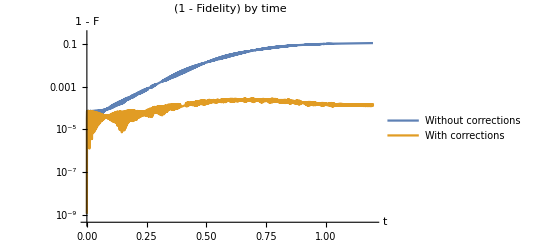

FINAL EVOLUTION OPERATOR

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | -0.000616816+0.00317536 ⅈ | 0.59264+0.805458 ⅈ | 0.000768544+0.00150474 ⅈ | 0.000194416+0.000181106 ⅈ | -0.000498501-0.000102927 ⅈ | 0.000438264+0.00103486 ⅈ | -1.76862×10^-7+1.19245×10^-6 ⅈ | 6.92103×10^-8+1.96497×10^-7 ⅈ
|g↓⇑> | 0.59264+0.805458 ⅈ | -0.00321792-0.00035879 ⅈ | 0.000844373+0.001371 ⅈ | 0.000253057-0.0000309881 ⅈ | 0.000238092+0.000401808 ⅈ | 0.000608934+0.00108662 ⅈ | 2.10984×10^-7+3.26974×10^-7 ⅈ | 2.35064×10^-7+8.51915×10^-8 ⅈ
|g↑⇓> | 0.000773062-0.00150243 ⅈ | 0.00062021-0.00148592 ⅈ | -0.423133+0.82481 ⅈ | 0.231552-0.172147 ⅈ | 0.00147867+0.0934295 ⅈ | -0.220295+0.0112662 ⅈ | -0.00075938+0.00102445 ⅈ | 0.0000103696-0.0000906435 ⅈ
|g↑⇑> | 0.0000335464-0.000263575 ⅈ | -0.000172889-0.00018737 ⅈ | 0.231552-0.172147 ⅈ | 0.807936+0.153571 ⅈ | -0.0261907-0.0942482 ⅈ | -0.385566+0.286658 ⅈ | 0.000282658-0.000332807 ⅈ | 0.000559451-0.000223871 ⅈ
|e↓⇓> | 0.000207446+0.000464826 ⅈ | 0.000187241-0.000427877 ⅈ | 0.00147867+0.0934295 ⅈ | -0.0261907-0.0942482 ⅈ | -0.36449-0.908039 ⅈ | -0.00243312-0.155899 ⅈ | -0.00130895-0.000266771 ⅈ | -0.0000161022-0.000137734 ⅈ
|e↓⇑> | 0.000584372-0.000959964 ⅈ | 0.000526755-0.00112874 ⅈ | -0.220295+0.0112662 ⅈ | -0.385566+0.286658 ⅈ | -0.00243312-0.155899 ⅈ | -0.188514+0.812809 ⅈ | 0.000259936-0.000709774 ⅈ | -0.0000169526+0.000151549 ⅈ
|e↑⇓> | -1.07408×10^-6-5.47343×10^-7 ⅈ | -3.77134×10^-7+9.58923×10^-8 ⅈ | 0.00127508+0.0000184968 ⅈ | -0.00043522-0.0000352084 ⅈ | 0.000547544+0.00121849 ⅈ | -0.00072802+0.000203305 ⅈ | -0.933535-0.35848 ⅈ | -0.00049506-0.0000845287 ⅈ
|e↑⇑> | -2.08307×10^-7+3.04265×10^-9 ⅈ | -1.55604×10^-7+1.95703×10^-7 ⅈ | -0.0000796483+0.0000444965 ⅈ | -0.000508359-0.000323535 ⅈ | -0.000102428+0.0000934798 ⅈ | 0.000132941-0.0000747067 ⅈ | -0.00049506-0.000084529 ⅈ | 0.999618-0.0276279 ⅈ)

Fidelity to σX: 0.999989

```mathematica
setVariables[]

ΔE = 0;
B0 = .20112299109490023;
Tmax = 1.1985082691258685*^-7;

Eamp[t_] := 220.15792727518044*tanhWindow[t, Tmax/10, Tmax]^2;
Bamp[t_] := 0.02844144148279332*tanhWindow[t, Tmax/10, Tmax]^2;
ωE = 3.430428865007686*^10;
ωB = 3.414701350724212*^10;

(* find true evolution *)
Uexact = findEvolutionOperator[Hexact];

(* approximate without corrections *)
U0 = ConjugateTranspose[Urot].findEvolutionOperator[HsimRot];

(* approximate with corrections *)
Ucorrected = ConjugateTranspose[Urot].findEvolutionOperator[Hcorrected];


LogPlot[{1 - fidelity[ConjugateTranspose[Uexact].U0], 1 - fidelity[ConjugateTranspose[Uexact].Ucorrected]}, {t, 0, Tmax}, PlotLegends->{"Without corrections", "With corrections"}, PlotLabel->"(1 - Fidelity) by time", AxesLabel->{"t", "1 - F"}]

Print["FINAL EVOLUTION OPERATOR"]
printWithBasis[Ucorrected /. t->Tmax, basisGE]

(* this was the state-averaged fidelity - is there a similar formula I should use for the 8x8 matrices? *)
fidelity2D[Mt_, Ma_] := (1/6)Sum[.25*Tr[Mt.(σI + σi).ConjugateTranspose[Mt].Ma.(σI + σi).ConjugateTranspose[Ma]], {σi, {σX, -σX, σY, -σY, σZ, -σZ}}] // Chop;
Print["Fidelity to σX: " <> ToString[fidelity2D[(Ucorrected /. t->Tmax)[[{1, 2}, {1, 2}]], σX]]]

clearVariables[]
```